I want to analytically solve for the vector magnetic feild (as a function of arbitrary position) for both a helix and a finite line
OverVector[dB] = (μ_0 I)/(4 π) (OverVector[dL] ×R⃗)/(|R⃗|^3)=(μ_0 I)/(4 π) (OverVector[dL]  ×R̂)/(|R⃗|^3) 
then B⃗(P)=∫OverVector[dB](P)
where 
I is the current
P is the observation location
R⃗ is the displacement vector from dL to P
R̂ is the unit vector of R⃗
dL is the infinitesimal wire element

We will set up the mechanisms by which any parametrized curve can be calculated

## Finite Wire

```mathematica
LineCyl[t_]:={0,0,t}
CylToCart[rθz_]:={rθz[[1]]  Cos[rθz[[2]] ],rθz[[1]]  Sin[rθz[[2]] ],rθz[[3]] }
LineCart=CylToCart [LineCyl[t]]
dLineCart=D[LineCart,t]
```

{0,0,t}

{0,0,1}

```mathematica
Pvec={px,py,pz};
Rvec=(Pvec-LineCart);
assum={{px,py,pz,t,Len}∈Reals,{Len}>0}
dB=Cross[dLineCart,Rvec]/Norm[Rvec]^3
```

{(px|py|pz|t|Len)∈ℝ,{Len}>0}

{-py/((Abs[px]^2+Abs[py]^2+Abs[pz-t]^2)^(3/2)),px/((Abs[px]^2+Abs[py]^2+Abs[pz-t]^2)^(3/2)),0}

```mathematica
Bindef=Integrate[dB,t,Assumptions->assum]
```

{-(py (-pz+t))/((px^2+py^2) √(px^2+py^2+(pz-t)^2)),(px (-pz+t))/((px^2+py^2) √(px^2+py^2+(pz-t)^2)),0}

Look for discontinuities in the antiderivative

```mathematica
Bindef[[1]]/.{t->x,pz->0,px->1,py->1}
```

-x/(2 √(2+x^2))

```mathematica
Bindef[[1]]/.{t->x,pz->0,px->1,py->1}
```

-x/(2 √(2+x^2))

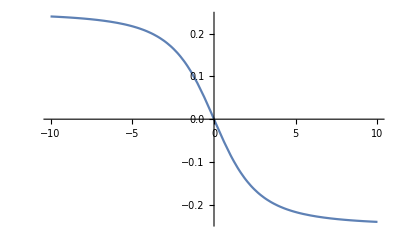

```mathematica
Plot[Bindef[[1]]/.{t->x,pz->0,px->2,py->2},{x,-10,10}]
```

```mathematica
Table[FullSimplify[(Bindef[[n]]/.t->tmax )-(Bindef[[n]]/.t->tmin)],
{n,{1,2,3}}]
```

{(py ((pz-tmax)/(√(px^2+py^2+(pz-tmax)^2))+(-pz+tmin)/(√(px^2+py^2+(pz-tmin)^2))))/(px^2+py^2),(px ((-pz+tmax)/(√(px^2+py^2+(pz-tmax)^2))+(pz-tmin)/(√(px^2+py^2+(pz-tmin)^2))))/(px^2+py^2),0}

solve the indefinite integral without concern for discontinuities

```mathematica
Bsol=Integrate[dB,{t,0,Len},Assumptions->assum,GenerateConditions->False]
```

{Piecewise[{{-(py (Len √(px^2+py^2+pz^2)-pz √(px^2+py^2+pz^2)+pz √(Len^2+px^2+py^2-2 Len pz+pz^2)))/((px^2+py^2) √(px^2+py^2+pz^2) √(Len^2+px^2+py^2-2 Len pz+pz^2)), Len>0}, {0, True}}],Piecewise[{{(px (Len √(px^2+py^2+pz^2)-pz √(px^2+py^2+pz^2)+pz √(Len^2+px^2+py^2-2 Len pz+pz^2)))/((px^2+py^2) √(px^2+py^2+pz^2) √(Len^2+px^2+py^2-2 Len pz+pz^2)), Len>0}, {0, True}}],0}

Let Mathematica solve the integral with the assumption that the probe point is not on the z axis

```mathematica
Bsol=FullSimplify[Integrate[dB,{t,0,Len},Assumptions->Append[assum,{Abs[px]+Abs[py]}>0]]]
```

{Piecewise[{{(py (-Len/(√(px^2+py^2+(Len-pz)^2))+pz (1/(√(px^2+py^2+(Len-pz)^2))-1/(√(px^2+py^2+pz^2)))))/(px^2+py^2), Len>0}, {0, True}}],Piecewise[{{(px (Len/(√(px^2+py^2+(Len-pz)^2))+pz (-1/(√(px^2+py^2+(Len-pz)^2))+1/(√(px^2+py^2+pz^2)))))/(px^2+py^2), Len>0}, {0, True}}],0}

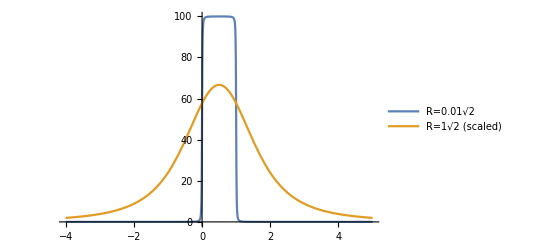

```mathematica
Plot[{Bsol[[2]]/.{px->0.01,py->0.01,pz->x,Len->1},
200*Bsol[[2]]/.{px->1,py->1,pz->x,Len->1}},{x,-4,5},PlotRange->All,PlotLegends->{"R=0.01√2","R=1√2 (scaled)"}]
```

Old attempt

```mathematica
dBk=Sin[ArcTan[rxy/Abs[zp-zs]]]/((zp-zs)^2+rxy^2)
```

rxy/((rxy^2+(zp-zs)^2) √(1+rxy^2/Abs[zp-zs]^2) Abs[zp-zs])

```mathematica
dBk=FullSimplify[dBk]
```

rxy/((rxy^2+(zp-zs)^2) √(rxy^2+Abs[zp-zs]^2))

```mathematica
indefsol=Integrate[ dBk,zs,Assumptions->{zp∈Reals,zs∈Reals,zs≥ 0,rxy∈Reals,rxy>0}]
```

(-zp+zs)/(rxy √(rxy^2+(zp-zs)^2))

```mathematica
indefsol/.{rxy->1,zp->0.9,zs->1}
```

0.100168

```mathematica
solution2=Integrate[ dBk,{zs,0,L},Assumptions->{zp∈Reals,zs∈Reals,zs≥ 0,rxy∈Reals,rxy>0,L∈Reals,L>0}]
```

(L √(rxy^2+zp^2)-zp √(rxy^2+zp^2)+zp √(L^2+rxy^2-2 L zp+zp^2))/(rxy √(rxy^2+zp^2) √(L^2+rxy^2-2 L zp+zp^2))

```mathematica
FullSimplify[Expand[solution2]]
```

(L/(√(rxy^2+(L-zp)^2))+zp (-1/(√(rxy^2+(L-zp)^2))+1/(√(rxy^2+zp^2))))/rxy

```mathematica
Limit[solution2/.zp->L/2,L->∞]
```

2/rxy

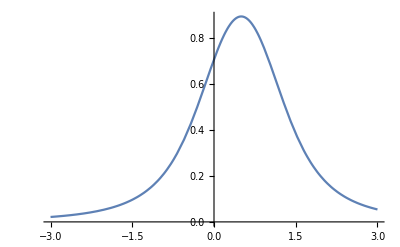

{0,0,1}

```mathematica
Plot[solution2/.{rxy->1,zp->x,L->1},{x,-3,3}]
```

## Helix

```mathematica
HelixCyl[t_]:={a,t,b t}
CylToCart[rθz_]:={rθz[[1]]  Cos[rθz[[2]] ],rθz[[1]]  Sin[rθz[[2]] ],rθz[[3]] }
HelixCart=CylToCart [HelixCyl[t]]
dHelixCart=D[HelixCart,t]
```

{a Cos[t],a Sin[t],b t}

{-a Sin[t],a Cos[t],b}

```mathematica
Pvec={px,py,pz};
Rvec=(Pvec-HelixCart);
assum={{px,py,pz,t,Len}∈Reals,{Len}>0}
dB=Cross[dHelixCart,Rvec]/Norm[Rvec]^3
FullSimplify[ExpandAll[dB],Assumptions->assum]
```

{(px|py|pz|t|Len)∈ℝ,{Len}>0}

{(-b py+a pz Cos[t]-a b t Cos[t]+a b Sin[t])/((Abs[pz-b t]^2+Abs[px-a Cos[t]]^2+Abs[py-a Sin[t]]^2)^(3/2)),(b px-a b Cos[t]+a pz Sin[t]-a b t Sin[t])/((Abs[pz-b t]^2+Abs[px-a Cos[t]]^2+Abs[py-a Sin[t]]^2)^(3/2)),(-a px Cos[t]+a^2 Cos[t]^2-a py Sin[t]+a^2 Sin[t]^2)/((Abs[pz-b t]^2+Abs[px-a Cos[t]]^2+Abs[py-a Sin[t]]^2)^(3/2))}

{(-b py+a (pz-b t) Cos[t]+a b Sin[t])/((Abs[pz-b t]^2+Abs[px-a Cos[t]]^2+Abs[py-a Sin[t]]^2)^(3/2)),(b px-a b Cos[t]+a (pz-b t) Sin[t])/((Abs[pz-b t]^2+Abs[px-a Cos[t]]^2+Abs[py-a Sin[t]]^2)^(3/2)),(a (a-px Cos[t]-py Sin[t]))/((Abs[pz-b t]^2+Abs[px-a Cos[t]]^2+Abs[py-a Sin[t]]^2)^(3/2))}

```mathematica
Bindef=Integrate[dB,t,Assumptions->assum]
```

{Integrate[(-b py+a pz Cos[t]-a b t Cos[t]+a b Sin[t])/((Abs[pz-b t]^2+Abs[px-a Cos[t]]^2+Abs[py-a Sin[t]]^2)^(3/2)),t,Assumptions→{(px|py|pz|t|Len)∈ℝ,{Len}>0}],Integrate[(b px-a b Cos[t]+a pz Sin[t]-a b t Sin[t])/((Abs[pz-b t]^2+Abs[px-a Cos[t]]^2+Abs[py-a Sin[t]]^2)^(3/2)),t,Assumptions→{(px|py|pz|t|Len)∈ℝ,{Len}>0}],Integrate[(-a px Cos[t]+a^2 Cos[t]^2-a py Sin[t]+a^2 Sin[t]^2)/((Abs[pz-b t]^2+Abs[px-a Cos[t]]^2+Abs[py-a Sin[t]]^2)^(3/2)),t,Assumptions→{(px|py|pz|t|Len)∈ℝ,{Len}>0}]}

```mathematica
FullSimplify[(Bindef[[1]]/.t->tmax )-(Bindef[[1]]/.t->tmin)]
```

(py ((pz-tmax)/(√(px^2+py^2+(pz-tmax)^2))+(-pz+tmin)/(√(px^2+py^2+(pz-tmin)^2))))/(px^2+py^2)

```mathematica
Bsol=Integrate[dB,{t,0,Len},Assumptions->assum,GenerateConditions->False]
```

{Piecewise[{{-(py (Len √(px^2+py^2+pz^2)-pz √(px^2+py^2+pz^2)+pz √(Len^2+px^2+py^2-2 Len pz+pz^2)))/((px^2+py^2) √(px^2+py^2+pz^2) √(Len^2+px^2+py^2-2 Len pz+pz^2)), Len>0}, {0, True}}],Piecewise[{{(px (Len √(px^2+py^2+pz^2)-pz √(px^2+py^2+pz^2)+pz √(Len^2+px^2+py^2-2 Len pz+pz^2)))/((px^2+py^2) √(px^2+py^2+pz^2) √(Len^2+px^2+py^2-2 Len pz+pz^2)), Len>0}, {0, True}}],0}